#### Preamble

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

```mathematica
SetDirectory[NotebookDirectory[]]
<<"MaTeX`"
<<"~/Documents/Wolfram/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"

fs = 11;
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
graphsOptsTeo= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215*.8, PlotStyle-> (Directive[Dashed,#]&/@colors)};
graphsOptsExp= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215*.8, PlotStyle-> (Directive[#]&/@colors)};
(*SetOptions[ListLinePlot,graphsOpts];*)
```

/home/juanathan/Documents/4.- UNAM-PCF-PhD/12-Protocolo/phD-protocolo/1-Calculos-Subtrate/1-Sample_Chracterization

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

## Diagramas

```mathematica
files = FileNames["*.txt","1-Distribuciones"][[;;5]];
data = Drop[Import[#,"Data"],2]/.{x_,y_}->{x*1*^9,y} & /@ files;  (*[[file, raddi, counts]]*)
thicknes = {3,3,3,5,5};

infoList = Append[#["ParameterTableEntries"][[;;,;;2]],#["RSquared"]]&;
legends[list_]:= MapThread[#1<>" -> "<> ToString[#2[[1]]]<>"±"<>ToString[#2[[2]]]<>"\n"&,{{"a","μ","σ"},Drop[list,-1]}];
```

#### Individual fits

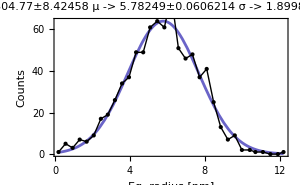
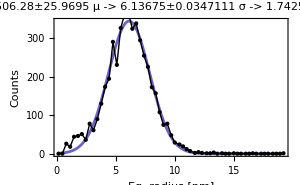
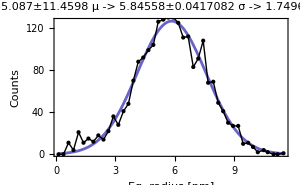
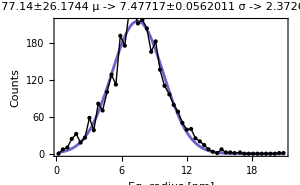
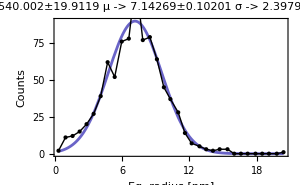

```mathematica
normal = a * PDF[NormalDistribution[mu,sigma],#]&;
fits = Map[NonlinearModelFit[#,normal[x],{a,mu,sigma},x]&,data];
info = Map[#["BestFitParameters"]&,fits];

MapThread[Plot[#1[x],{x,#2[[1,1]],#2[[-1,1]]},
PlotRange->Full,Epilog ->{Point[#2],Line[#2]},
PlotLabel->(Style[StringJoin@legends[infoList[#1]],texStyle]),
Evaluate[graphsOptsExp],
FrameLabel->{"Eq. radius [nm]","Counts"}
]&,{fits,data}]
```

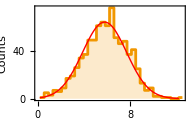
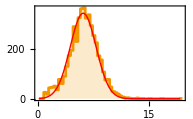
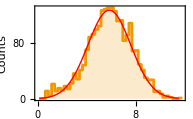
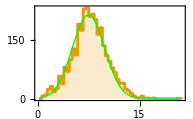
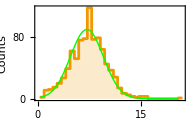

```mathematica
texStyle={FontFamily->"Latin Modern Math",FontSize->fs, Bold};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
graphsOptsExp= {Mesh-> None,BaseStyle-> texStyle,Frame-> {{True,False},{True,False}}, FrameStyle-> Directive[Thickness[.005],White],ImageSize-> 215*.9, PlotStyle-> (Directive[#]&/@colors)};
(*SetOptions[ListLinePlot,graphsOpts];*)

plots = MapThread[Show[{
ListStepPlot[#2,PlotStyle->colors[[3]], Filling->Bottom, Evaluate[graphsOptsExp],FrameLabel->{"Eq. radius [nm]","Counts"}
 (* Prolog->{Opacity[.1],Inset[#3,Center,Center,Scaled[1.25]]}*)],
Plot[#1[x],{x,#2[[1,1]],#2[[-1,1]]},PlotStyle->Directive[Thick,#3]]}
]&,{fits,data,{Red,Red,Red,Green,Green}}]
```

```mathematica
MapIndexed[Export[FileNameJoin[{"2-SEM","plot_"<>ToString[First[#2]]<>".svg"}],#1]&,plots]
```

{2-SEM/plot_1.svg,2-SEM/plot_2.svg,2-SEM/plot_3.svg,2-SEM/plot_4.svg,2-SEM/plot_5.svg}